```mathematica
data=Select[Import["/home/nils/uni/Papers/2017/input-transformations/experiments/aggregated","TSV"],Length[#]==12&];
```

```mathematica
groupedData=GroupBy[data,{#[[4]],#[[5]],#[[6]],#[[7]],#[[8]]}&];
```

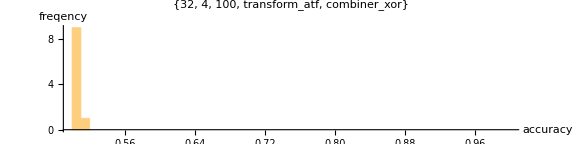
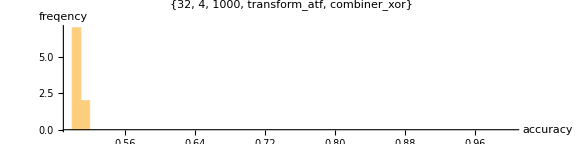
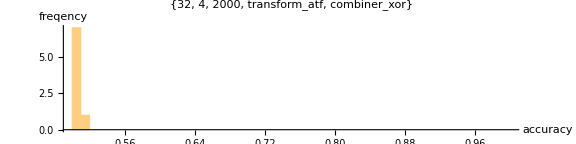
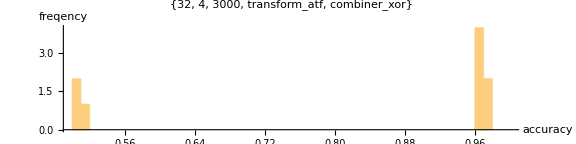
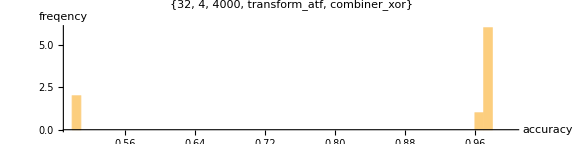
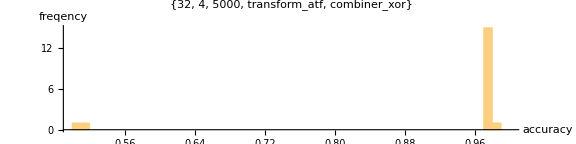
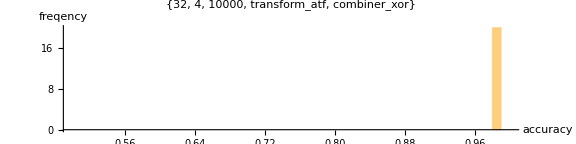
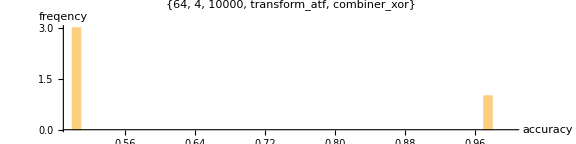

```mathematica
Table[
Histogram[
groupedData[group][[All,11]],
{.5,1,.01},
ImageSize->Large,
AxesLabel->{"accuracy","freqency"},
PlotRange->Full,
AspectRatio->1/4,
PlotLabel->ToString[group]
],
{group,SortBy[Keys[groupedData],#[[3]]&]}
]
```